```mathematica
alphaH[V_]:=0.07*E^(-V/20)
betaH[V_]=1/(E^((30-V)/10)+1)
h0[V_]=alphaH[V]/(alphaH[V]+betaH[V])

alphaM[V_]=((0.1*(25-V))/(E^((25−V)/10)−1))
betaM[V_]=(4*E^(-V/18))
m0[V_]=alphaM[V]/(alphaM[V]+betaM[V])

alphaN[V_]=(0.01*(10-V))/(E^((10-V)/10)-1)
betaN[V_]=0.125*E^(-V/80)
n0[V_]=alphaN[V]/(alphaN[V]+betaN[V])

τm[V_]=1/(alphaM[V]+betaM[V])
τn[V_]=1/(alphaN[V]+betaN[V])
τh[V_]=1/(alphaH[V]+betaH[V])

GK=34
VK=-11
JK[V_]=GK*n0[V]^4*(V-VK)

GNa=120
VNa=109
JNa[V_]=GNa*m0[V]*h0[V]*(V-VNa)

curent=50
```

1/(1+ⅇ^((30-V)/10))

(0.07 ⅇ^(-V/20))/(0.07 ⅇ^(-V/20)+1/(1+ⅇ^((30-V)/10)))

(0.1 (25-V))/(-1+ⅇ^((25-V)/10))

4 ⅇ^(-V/18)

(0.1 (25-V))/((-1+ⅇ^((25-V)/10)) (4 ⅇ^(-V/18)+(0.1 (25-V))/(-1+ⅇ^((25-V)/10))))

(0.01 (10-V))/(-1+ⅇ^((10-V)/10))

0.125 ⅇ^(-V/80)

(0.01 (10-V))/((-1+ⅇ^((10-V)/10)) (0.125 ⅇ^(-V/80)+(0.01 (10-V))/(-1+ⅇ^((10-V)/10))))

1/(4 ⅇ^(-V/18)+(0.1 (25-V))/(-1+ⅇ^((25-V)/10)))

1/(0.125 ⅇ^(-V/80)+(0.01 (10-V))/(-1+ⅇ^((10-V)/10)))

1/(0.07 ⅇ^(-V/20)+1/(1+ⅇ^((30-V)/10)))

34

-11

(3.4×10^-7 (10-V)^4 (11+V))/((-1+ⅇ^((10-V)/10))^4 (0.125 ⅇ^(-V/80)+(0.01 (10-V))/(-1+ⅇ^((10-V)/10)))^4)

120

109

(0.84 ⅇ^(-V/20) (25-V) (-109+V))/((-1+ⅇ^((25-V)/10)) (0.07 ⅇ^(-V/20)+1/(1+ⅇ^((30-V)/10))) (4 ⅇ^(-V/18)+(0.1 (25-V))/(-1+ⅇ^((25-V)/10))))

50

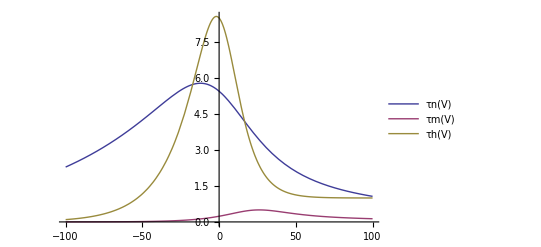

```mathematica
Plot[{τn[V],τm[V],τh[V]},{V,-100,100},PlotRange->All,PlotLegends->"Expressions"]
```

{{m[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

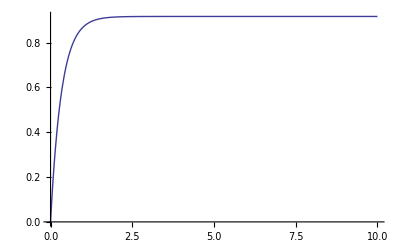

```mathematica
difm=NDSolve[{m'[t]==-(m[t]-m0[curent])/(τm[curent]),m[0]==0},m[t],{t,0,10}]
Plot[Evaluate[m[t]/.difm],{t,0,10},PlotRange->All]
```

{{H[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

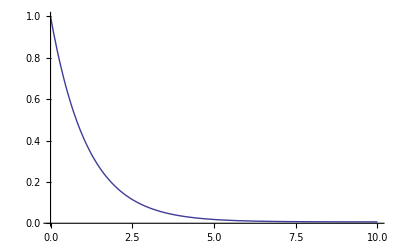

```mathematica
difh=NDSolve[{H'[t]==-(H[t]-h0[curent])/(τh[curent]),H[0]==1},H[t],{t,0,10}]
Plot[Evaluate[H[t]/.difh],{t,0,10},PlotRange->All]
```

{{n[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

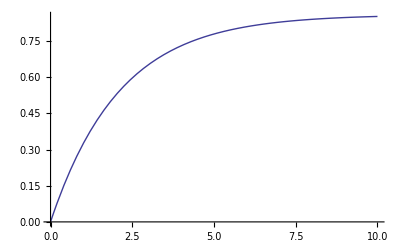

```mathematica
difn=NDSolve[{n'[t]==-(n[t]-n0[curent])/(τn[curent]),n[0]==0},n[t],{t,0,10}]
Plot[Evaluate[n[t]/.difn],{t,0,10},PlotRange->All]
```